```mathematica
(*Mathematica*)
```

```mathematica
d[n_]=1/Im[ZetaZero[n]]
```

1/Im[ZetaZero[n]]

```mathematica
p[x_,n_]=ExpandAll[(x+1/(1+d[n]))*(x-(1+d[n]))]
```

-x+x^2-1/(1+1/Im[ZetaZero[n]])+x/(1+1/Im[ZetaZero[n]])-x/Im[ZetaZero[n]]-1/((1+1/Im[ZetaZero[n]]) Im[ZetaZero[n]])

```mathematica
q[x_,n_]=ExpandAll[x^n*p[1/x,n]]
```

x^(-2+n)-x^(-1+n)-x^n/(1+1/Im[ZetaZero[n]])+x^n/(x+x/Im[ZetaZero[n]])-x^(-1+n)/Im[ZetaZero[n]]-x^n/(1+Im[ZetaZero[n]])

```mathematica
(*f[x_]=Product[N[1/q[x,n]],{n,300}];*)
```

```mathematica
g[x_]=Product[N[1/p[x,n]],{n,300}];
```

```mathematica
(*Table[SeriesCoefficient[Series[1/f[x],{x,0,100}],m],{m,0,200}]*)
```

```mathematica
(*expansion sequence of Imaginary ZetaZero's*)
```

```mathematica
a=Table[SeriesCoefficient[Series[1/g[x],{x,0,300}],m],{m,0,300}]
```

{1.,3.11027,-295.205,-925.084,43424.7,137116.,-4.24399×10^6,-1.35038×10^7,3.10015×10^8,9.94106×10^8,-1.80545×10^10,-5.83497×10^10,8.73184×10^11,2.84445×10^12,-3.60722×10^13,-1.18452×10^14,1.29938×10^15,4.30153×10^15,-4.14598×10^16,-1.38379×10^17,1.18642×10^18,3.99279×10^18,-3.07559×10^19,-1.04376×10^20,7.28274×10^20,2.49254×10^21,-1.5862×10^22,-5.47548×10^22,3.19662×10^23,1.11305×10^24,-5.99112×10^24,-2.10441×10^25,1.04891×10^26,3.7171×10^26,-1.72217×10^27,-6.15785×10^27,2.66085×10^28,9.60072×10^28,-3.88067×10^29,-1.41308×10^30,5.35716×10^30,1.96887×10^31,-7.01754×10^31,-2.60337×10^32,8.74253×10^32,3.27418×10^33,-1.03797×10^34,-3.92475×10^34,1.17663×10^35,4.49241×10^35,-1.27571×10^36,-4.91874×10^36,1.32499×10^37,5.1597×10^37,-1.32025×10^38,-5.19313×10^38,1.26378×10^39,5.02179×10^39,-1.16361×10^40,-4.67154×10^40,1.03174×10^41,4.18548×10^41,-8.81952×10^41,-3.6157×10^42,7.27561×10^42,3.01471×10^43,-5.79779×10^43,-2.42842×10^44,4.46702×10^44,1.89156×10^45,-3.33045×10^45,-1.42595×10^46,2.40473×10^46,1.04118×10^47,-1.68281×10^47,-7.36903×10^47,1.14214×10^48,5.0591×10^48,-7.52338×10^48,-3.37138×10^49,4.81277×10^49,2.18219×10^50,-2.99178×10^50,-1.37276×10^51,1.80828×10^51,8.39774×10^51,-1.06327×10^52,-4.99849×10^52,6.08544×10^52,2.89635×10^53,-3.39176×10^53,-1.63462×10^54,1.84183×10^54,8.98972×10^54,-9.74911×10^54,-4.81986×10^55,5.0322×10^55,2.52043×10^56,-2.53402×10^56,-1.28601×10^57,1.24536×10^57,6.40506×10^57,-5.9755×10^57,-3.11512×10^58,2.80034×10^58,1.47999×10^59,-1.2822×10^59,-6.87115×10^59,5.73791×10^59,3.11842×10^60,-2.51042×10^60,-1.38394×10^61,1.07416×10^61,6.00775×10^61,-4.49626×10^61,-2.55182×10^62,1.84169×10^62,1.06087×10^63,-7.38391×10^62,-4.31779×10^63,2.89852×10^63,1.72097×10^64,-1.11428×10^64,-6.71904×10^64,4.19619×10^64,2.57024×10^65,-1.5483×10^65,-9.63556×10^65,5.59885×10^65,3.54095×10^66,-1.98463×10^66,-1.27585×10^67,6.89752×10^66,4.5083×10^67,-2.35086×10^67,-1.56261×10^68,7.85903×10^67,5.31374×10^68,-2.57752×10^68,-1.77317×10^69,8.29485×10^68,5.8074×10^69,-2.61978×10^69,-1.86714×10^70,8.12174×10^69,5.89402×10^70,-2.4719×10^70,-1.8271×10^71,7.38728×10^70,5.56293×10^71,-2.16809×10^71,-1.66381×10^72,6.24989×10^71,4.88917×10^72,-1.76985×10^72,-1.41176×10^73,4.92416×10^72,4.00633×10^73,-1.34622×10^73,-1.11752×10^74,3.61702×10^73,3.06442×10^74,-9.55185×10^73,-8.26195×10^74,2.47961×10^74,2.19037×10^75,-6.32832×10^74,-5.71093×10^75,1.58802×10^75,1.46455×10^76,-3.9186×10^75,-3.69459×10^76,9.50966×10^75,9.16934×10^76,-2.26987×10^76,-2.23909×10^77,5.32949×10^76,5.38042×10^77,-1.23101×10^77,-1.27237×10^78,2.79747×10^77,2.96153×10^78,-6.25522×10^77,-6.78517×10^78,1.37635×10^78,1.53036×10^79,-2.98032×10^78,-3.39824×10^79,6.35155×10^78,7.42993×10^79,-1.33234×10^79,-1.59964×10^80,2.75106×10^79,3.39161×10^80,-5.59202×10^79,-7.08227×10^80,1.11906×10^80,1.45665×10^81,-2.20485×10^80,-2.95117×10^81,4.27742×10^80,5.89002×10^81,-8.17117×10^80,-1.15813×10^82,1.53715×10^81,2.24363×10^82,-2.84774×10^81,-4.28279×10^82,5.19595×10^81,8.05586×10^82,-9.33755×10^81,-1.49327×10^83,1.65283×10^82,2.72791×10^83,-2.88184×10^82,-4.91156×10^83,4.94976×10^82,8.71625×10^83,-8.37509×10^82,-1.52471×10^84,1.39607×10^83,2.62916×10^84,-2.29275×10^83,-4.46932×10^84,3.70987×10^83,7.49005×10^84,-5.91468×10^83,-1.23757×10^85,9.29167×10^83,2.01612×10^85,-1.43835×10^84,-3.23853×10^85,2.19414×10^84,5.12959×10^85,-3.29845×10^84,-8.01201×10^85,4.88678×10^84,1.23408×10^86,-7.13546×10^84,-1.87457×10^86,1.0269×10^85,2.80828×10^86,-1.45669×10^85,-4.14929×10^86,2.03684×10^85,6.04669×10^86,-2.80756×10^85,-8.69136×10^86,3.81511×10^85,1.23225×10^87,-5.11122×10^85,-1.72332×10^87,6.75172×10^85,2.37739×10^87,-8.79457×10^85,-3.23532×10^87,1.12971×10^86,4.34338×10^87,-1.43128×10^86,-5.75236×10^87,1.78869×10^86,7.5159×10^87,-2.20527×10^86,-9.68824×10^87,2.68271×10^86,1.2321×10^88,-3.2207×10^86,-1.54595×10^88,3.8166×10^86,1.91383×10^88,-4.4653×10^86,-2.33762×10^88,5.15919×10^86,2.81721×10^88,-5.8883×10^86,-3.35001×10^88,6.64057×10^86,3.9306×10^88,-7.40238×10^86,-4.55057×10^88,8.15907×10^86,5.19842×10^88,-8.89556×10^86,-5.8598×10^88,9.59703×10^86,6.51782×10^88,-1.02495×10^87,-7.15379×10^88,1.08401×10^87,7.74795×10^88,-1.13579×10^87,-8.28052×10^88,1.17936×10^87,8.73275×10^88,-1.21397×10^87,-9.08802×10^88,1.23908×10^87,9.33284×10^88,-1.25429×10^87,-9.45771×10^88,1.25938×10^87}

```mathematica
(*ratios of the sequence*)
```

```mathematica
ro=Table[a[[n+1]]/a[[n]],{n,Length[a]-1}]
```

{3.11027,-94.9129,3.1337,-46.9414,3.15757,-30.9517,3.18187,-22.9575,3.20664,-18.1616,3.23186,-14.9647,3.25757,-12.6816,3.28376,-10.9696,3.31046,-9.63839,3.33767,-8.5737,3.36541,-7.70286,3.39369,-6.9774,3.42253,-6.36379,3.45194,-5.83806,3.48194,-5.38264,3.51255,-4.98435,3.54377,-4.6331,3.57563,-4.32107,3.60815,-4.04206,3.64133,-3.79112,3.67521,-3.56425,3.7098,-3.35816,3.74512,-3.17015,3.7812,-2.99796,3.81804,-2.8397,3.85569,-2.69375,3.89415,-2.55876,3.93346,-2.43355,3.97364,-2.31711,4.01471,-2.20857,4.05671,-2.10717,4.09965,-2.01223,4.14358,-1.92317,4.18852,-1.83948,4.23449,-1.76069,4.28155,-1.68641,4.32971,-1.61626,4.37901,-1.54992,4.4295,-1.4871,4.4812,-1.42754,4.53417,-1.371,4.58843,-1.31726,4.64404,-1.26614,4.70104,-1.21746,4.75948,-1.17105,4.8194,-1.12676,4.88085,-1.08447,4.9439,-1.04406,5.00859,-1.00539,5.07499,-0.968385,5.14315,-0.932935,5.21314,-0.898952,5.28503,-0.866357,5.35888,-0.835073,5.43477,-0.80503,5.51277,-0.776162,5.59297,-0.74841,5.67544,-0.721715,5.76028,-0.696027,5.84757,-0.671296,5.93741,-0.647475,6.02991,-0.624522,6.12517,-0.602397,6.2233,-0.581062,6.32442,-0.560481,6.42864,-0.540622,6.53611,-0.521452,6.64695,-0.502944,6.76131,-0.485068,6.87935,-0.467799,7.0012,-0.451112,7.12706,-0.434984,7.25709,-0.419392,7.39147,-0.404317,7.53042,-0.389738,7.67412,-0.375636,7.82281,-0.361995,7.97671,-0.348796,8.13607,-0.336024,8.30114,-0.323665,8.47222,-0.311702,8.64958,-0.300124,8.83353,-0.288916,9.0244,-0.278066,9.22255,-0.267563,9.42833,-0.257394,9.64214,-0.24755,9.8644,-0.23802,10.0956,-0.228794,10.3361,-0.219862,10.5864,-0.211216,10.8472,-0.202847,11.119,-0.194746,11.4023,-0.186907,11.6978,-0.17932,12.0063,-0.17198,12.3284,-0.164878,12.665,-0.158008,13.0168,-0.151364,13.3849,-0.14494,13.77,-0.138729,14.1734,-0.132726,14.5961,-0.126925,15.0392,-0.121322,15.5041,-0.11591,15.9921,-0.110685,16.5046,-0.105643,17.0431,-0.100778,17.6095,-0.0960859,18.2053,-0.091563,18.8326,-0.0872049,19.4932,-0.0830076,20.1895,-0.0789672,20.9237,-0.0750801,21.6981,-0.0713426,22.5155,-0.0677511,23.3786,-0.0643025,24.2902,-0.0609932,25.2533,-0.0578203,26.2712,-0.0547806,27.3471,-0.0518711,28.4844,-0.0490889,29.6866,-0.0464313,30.957,-0.0438955,32.2992,-0.0414788,33.7163,-0.0391786,35.2116,-0.0369926,36.7877,-0.0349182,38.4468,-0.032953,40.1904,-0.0310948,42.0192,-0.0293413,43.9323,-0.0276904,45.9275,-0.0261399,48.0006,-0.0246877,50.1449,-0.0233318,52.3509,-0.0220703,54.6057,-0.0209011,56.8926,-0.0198226,59.1907,-0.0188327,61.4744,-0.0179298,63.7135,-0.017112,65.8733,-0.0163778,67.915,-0.0157253,69.7967,-0.015153,71.4747,-0.0146593,72.9052,-0.0142426,74.0466,-0.0139014,74.8619,-0.0136342,75.321,-0.0134395,75.4031,-0.0133159}

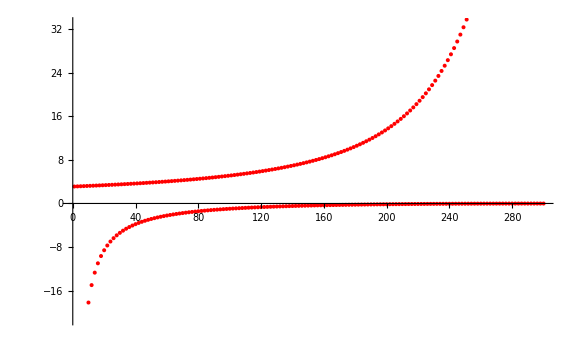

```mathematica
ListPlot[ro,PlotStyle->{Red,PointSize[0.005]},ImageSize->Large]
```

```mathematica
(*end*)
```